```mathematica
ColorDistance[#,ColorConvert[#,"RGB"]]&@LCHColor[.5,.2,0]
```

1.09515×10^-6

```mathematica
ColorConvert[LCHColor[1,1,0],"RGB"]//InputForm
```

RGBColor[1., 0.5951806925096235, 1.]

```mathematica
RGBColor[1., 0.5951806925096235, 1.]
```

RGBColor[1., 0.5951806925096235, 1.]

```mathematica
LCHColor[1,1,0]
```

LCHColor[1, 1, 0]

```mathematica
ColorConvert[RGBColor[1., 0.5951806925096235, 1.],"LCH"]//InputForm
```

LCHColor[0.7652541956959736, 0.6139405020021171, 0.9036707601557563]

```mathematica
cc[RGBColor[r_Real|r_Integer,g_Real|g_Integer,b_Real|b_Integer],sp_]:=ColorConvert[RGBColor[r,g,b],sp]
cc[LCHColor[r_Real|r_Integer,g_Real|g_Integer,b_Real|b_Integer],sp_]:=ColorConvert[LCHColor[r,g,b],sp]
```

```mathematica
cdrl[RGBColor[r_Real|r_Integer,g_Real|g_Integer,b_Real|b_Integer],
LCHColor[l_Real|l_Integer,c_Real|c_Integer,h_Real|h_Integer]]:=ColorDistance[RGBColor[r,g,b],LCHColor[l,c,h]]
```

```mathematica
cdlr[LCHColor[l_Real|l_Integer,c_Real|c_Integer,h_Real|h_Integer],
RGBColor[r_Real|r_Integer,g_Real|g_Integer,b_Real|b_Integer]]:=ColorDistance[LCHColor[l,c,h],RGBColor[r,g,b]]
```

```mathematica
prec=10^-2.
```

0.01

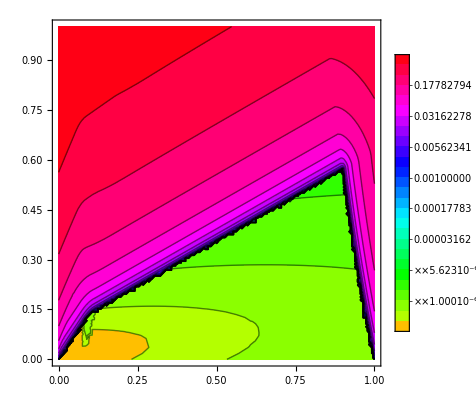

```mathematica
ContourPlot[Evaluate[cdlr[#,cc[#,"RGB"]]&@LCHColor[l,c,.5]],{l,0,1},{c,0,1},PlotLegends->Automatic,Contours->10^Range[-6.5,0,.25],ColorFunction->Function[x,Hue[Log10[10^-7+x]/8]]]
```

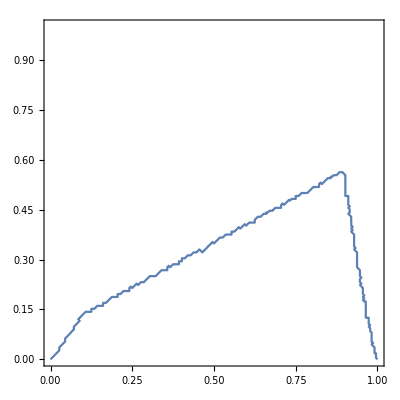

```mathematica
ContourPlot[
cdlr[LCHColor[l,c,.5],cc[LCHColor[l,c,.5],"RGB"]]==10^-5,
{l,0,1},{c,0,1},PlotLegends->Automatic]
```

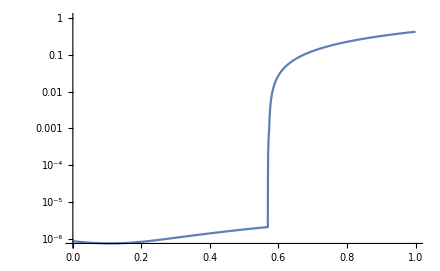

```mathematica
LogPlot[Evaluate[cdlr[#,cc[#,"RGB"]]&@LCHColor[.9,c,.5]],{c,0,1}]
```

```mathematica
NMaximize[{cdrl[RGBColor[r,g,b],cc[RGBColor[r,g,b],"LCH"]],0≤r≤1,0≤g≤1,0≤b≤1},{r,g,b}]
```

{8.00593×10^-16,{r→0.271241,g→0.0926199,b→0.611267}}

```mathematica
cdrl[RGBColor[r,g,b],cc[RGBColor[r,g,b],"LCH"]]/.{r->.5,g->.5,b->.5}
```

2.95941×10^-23

```mathematica
NMaximize[{cdrl[cc[cc[RGBColor[r,g,b],"LCH"],"RGB"],cc[RGBColor[r,g,b],"LCH"]],0≤r≤1,0≤g≤1,0≤b≤1},{r,g,b}]
```

{2.63932×10^-6,{r→0.0000132524,g→0.320447,b→0.995902}}

```mathematica
(* conclusion: 2.64e-6 is the highest error from L->R conversion for an sRGB color. R->L conversion is always much lower-error. *)
```

```mathematica
RGBColor[r,g,b]/.{r->0.000013252437650560812,g->0.32044729785791426,b->0.9959020959453162}
```

RGBColor[0.000013252437650560812, 0.32044729785791426, 0.9959020959453162]

```mathematica
(* "Inaccurate Blue" *)
```

```mathematica
rgbQ[c_LCHColor]:=cdlr[c,cc[c,"RGB"]]<10^-5
```

```mathematica
maxchroma[hues_,l_]:=NMaximize[{c,Fold[And,True,rgbQ[LCHColor[l,c,#]]&/@hues]},c][[1]]
```

```mathematica
maxpal[hues_,l_]:=LCHColor[l,maxchroma[hues,l],#]&/@hues
```

```mathematica
maxpal[{0,.5},.8]
```

{LCHColor[0.8, 0.32300286658453325, 0],LCHColor[0.8, 0.32300286658453325, 0.5]}

```mathematica
maxchroma[{0,.5},.5]
```

0.356679

```mathematica
Plot[maxchroma[{0,.5},l],{l,0,1}]
```

$Aborted